```mathematica
(*Approximation de la probabilité de ruine ultime*)
(*Developpement de densité de probabilité bivariée*)
(*La mesure de référence choisi est la loi Gamma de paramètre ξ et ν*)
muGamma=Function[{x,m,r},(1/m)^(r)*Exp[-x/m]*x^(r-1)/Gamma[r]];
(*Polynôme mu orthogonaux associé*)
QnGamma=Function[{n,x,m,r},(-1)^n*LaguerreL[n,r-1,x/m]/Sqrt[Binomial[n+r-1,n]]];
(*Loi binomial negative de paramètre a et p*)
FoncGenPoisson=Function[{s,λ},Exp[-λ(s-1)]-Exp[-λ]];
(*Distribution PhaseType*)
LaplacePhaseType=Function[{s,α,T,t,k},α.(Inverse[s*IdentityMatrix[k]-T]).t];
LaplaceCompoundPoissonPhaseType=Function[{s,λ,α,T,t,k},FoncGenPoisson[LaplacePhaseType[s,α,T,t,k],λ]];
CoefGenFunctionCompoundPoissonPhaseType=Function[{λ,α,T,t,k,z,m,r},FullSimplify[(1-z)^(-r)*LaplaceCompoundPoissonPhaseType[z/m/(1-z),λ,α,T,t,k]]];
ExpansionCoefficientCompoundPoissonPhaseType=Function[{λ,α,T,t,k,z,m,r,K},Expansion=Normal[Series[CoefGenFunctionCompoundPoissonPhaseType[λ,α,T,t,k,z,m,r],{z,0,K}]];Table[(-1)^(i)/Sqrt[Binomial[i+r-1,i]]/(i!)*(D[Expansion,{z,i}]/.z->0),{i,0,K}]];
(*Probabilité de ruine pour les phase type*)
DensityCompoundPoissonExponential=Function[{x,λ,δ},Exp[-(λ+x*δ)]*2*Sqrt[λ*δ/x]*BesselI[1,2λ*δ*x]];
(*Système de polynômes orthogonaux*)
Qnm=Function[{x,m,r,K},Table[QnGamma[i,x,m,r]muGamma[x,m,r],{i,0,K}]];
DensityExpansion=Function[{VectorCoef,VectorPoly},Total[VectorCoef*VectorPoly]];
(*Evaluation de la probabilité de ruine via ls FFT*)
(*Fonction de sur£vie via les FFT*)
(*Calcul des Sn*)
FoncGenPoissonFFT=Function[{s,λ},Exp[-λ(s-1)]];
LaplaceCompoundPoissonPhaseTypeSurvival=Function[{s,λ,α,T,t,k},(1-FoncGenNegBinFFT[LaplacePhaseType[s,α,T,t,k],λ])/s];
SnCompoundPoissonPhaseTypeDensity=Function[{b,x,n,λ,α,T,t,k},Exp[b/2]/2/x*Re[LaplaceCompoundPoissonPhaseType[b/2/x,λ,α,T,t,k]]+Exp[b/2]/x*Sum[(-1)^(i)*Re[LaplaceCompoundPoissonPhaseType[(b+I*i*2π)/2/x,λ,α,T,t,k]],{i,1,n,1}]];
SnCompoundPoissonPhaseTypeSurvival=Function[{b,u,n,λ,α,T,t,k},Exp[b/2]/2/u*Re[LaplaceCompoundPoissonPhaseTypeSurvival[b/2/u,λ,α,T,t,k]]+Exp[b/2]/u*Sum[(-1)^(i)*Re[LaplaceCompoundPoissonPhaseTypeSurvival[(b+I*i*2π)/2/u,λ,α,T,t,k]],{i,1,n,1}]];
DensityCompoundPoissonPhaseTypeFFT=Function[{m,b,x,n,λ,α,T,t,k},Sum[Binomial[m,i]*2^(-m)SnCompoundPoissonPhaseTypeDensity[b,x,n+i,λ,α,T,t,k],{i,0,m,1}]];
SurvivalCompoundPoissonPhaseTypeFFT=Function[{m,b,u,n,λ,α,T,t,k},Sum[Binomial[m,i]*2^(-m)SnCompoundPoissonPhaseTypeSurvival[b,u,n+i,λ,α,T,t,k],{i,0,m,1}]];
(*Evaluation de la probabilité de ruine via la scaled laplace Transform*)
LaplaceRuinProbaPhaseTypeMnats=Function[{s,p,λ,c,α,T,t,k},1/s-(1-p)/(s-λ/c(1-LaplacePhaseType[s,α,T,t,k]))]
(*Formule de la densité et transformée de Laplace de la probabilité de ruine*)
RuinProbaPhaseTypeMnats=Function[{p,λ,c,α,T,t,k,αMnats,bMnats,i},Log[bMnats]*(αMnats+1)Binomial[αMnats-1,i-1]*Sum[Binomial[i-1,j]*(-1)^(j)*LaplaceRuinProbaPhaseTypeMnats[(j+αMnats-i+1)Log[bMnats],p,λ,c,α,T,t,k],{j,0,i-1}]];
RuinProbaPhaseTypeMnats2=Function[{p,λ,c,α,T,t,k,αMnats,u},Exp[-u]*Gamma[αMnats+2]/Gamma[Floor[αMnats*Exp[-u]]+1]*(*αMnats/(αMnats+1)*)Sum[(-1)^(j)*LaplaceRuinProbaPhaseTypeMnats[j+Floor[αMnats*Exp[-u]],p,λ,c,α,T,t,k]/j!
/(αMnats-Floor[αMnats*Exp[-u]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-u]]}]
]
(*Algorithme de Panjer*)
(*Discrétisation, h représente le pas de discrétisation, u est la limite, on créer un vecteur de taille u/h*)
CDFPhaseTypeI=Function[{α,T,e,y},1-Integrate[α.MatrixExp[T*w].e,{w,y,+∞}]/(-α.Inverse[T].e)];
DiscretizePhaseType=Function[{α,T,e,umax,h},PartitionGrid=Table[k*h,{k,0,umax/h,1}];ProbaUI=Table[N[CDFPhaseTypeI[α,T,e,Max[PartitionGrid[[i]]+h/2,0]]-CDFPhaseTypeI[α,T,e,Max[PartitionGrid[[i]]-h/2,0]]],{i,1,Length[PartitionGrid](*-1*),1}]];
ProbaDiscreteGeometricCompoundPhaseType=Function[{p,h,VectProbaUI,umax},ProbaCompoundGeo={};AppendTo[ProbaCompoundGeo,1-p];
For[j=1,j<umax/h+1,j++,AppendTo[ProbaCompoundGeo,Sum[p*VectProbaUI[[k]]*ProbaCompoundGeo[[(j-k)+1]],{k,1,j,1}]]];ProbaCompoundGeo];
RuinProbaPangerPhaseType=Function[{VectProbaCompoundGeo,h,u},1-Sum[VectProbaCompoundGeo[[k]],{k,1,u/h}]];
```

Function[{s,p,λ,c,α,T,t,k},1/s-(1-p)/(s-(λ (1-LaplacePhaseType[s,α,T,t,k]))/c)]

Function[{p,λ,c,α,T,t,k,αMnats,u},(Exp[-u] Gamma[αMnats+2] ∑_(j=0)^(αMnats-Floor[αMnats Exp[-u]]) ((-1)^j LaplaceRuinProbaPhaseTypeMnats[j+Floor[αMnats Exp[-u]],p,λ,c,α,T,t,k])/(j! (αMnats-Floor[αMnats Exp[-u]]-j)!))/Gamma[Floor[αMnats Exp[-u]]+1]]

```mathematica
(*cas Phase type Erlang(2,1) *)
(*Paramètre de la distribution: formalisme phase type*)
δ1=1;
δ2=1;
δ3=5;
(*T={{-δ1,δ1,0,0,0},{0,-δ1,δ1,0,0},{0,0,-δ1,0,0},{0,0,0,-δ2,δ2},{0,0,0,0,-δ2}};*)(*Mélange de Erlang*)
T={{-δ1,δ1,0},{0,-δ1,δ1},{0,0,-δ1}};(*Mélange d'exponentielle*)
MatrixForm[T];
(*t={0,0,δ1,0,δ2};*)(*Mélange de Erlang*)
t={0,0,δ1};(*Mélange d'exponentielle*)
(*e={1,1,1,1,1};*)(*Mélange de Erlang*)
e={1,1,1};(*Mélange d'exponentielle*)
(*α={1/2,0,0,1/2,0};*)(*Mélange d'Erlang*)
α={1,0,0};(*Mélange d'exponentielle*)
N[μ=-α.Inverse[T].e]
(*Clear[μ]*)
k=3;
(*Intensité du processus de Poisson*)
λ=1;
(*Safety loading*)
(*η=20/100*)
(*Premium*)
c=5;
N[λ/c]
p=λ*μ/c;
(*Clear[λ]*)
(*Chargement de sécurité et niveau des primes*)
N[η=p^(-1)-1]
(*Clear[c]*)
(*Clear[p]*)
αPlus=-(p/μ)*α.Inverse[T];
Q=T+KroneckerProduct[t,αPlus];
N[Sol=Solve[LaplacePhaseTypeI[-s,α,T,e,k]==p^(-1),s]]
```

3.

0.2

0.666667

{{s→0.217627},{s→1.29119+0.413332 ⅈ},{s→1.29119-0.413332 ⅈ}}

```mathematica
(*Paramétrisation du développement polynomial*)
m={N[1000/442],N[1000/441],N[1000/441]*4/5,N[1000/441]*4/7}
r={1,1,1,1};
NbParametrization=1;
ParameterString={"2/γ","1/γ","4/(5γ)","4/(7γ)"};
```

{2.26244,2.26757,1.81406,1.29576}

```mathematica
(*Coefficient du développement et polynômes orthogonaux*)
(*Coefficient du développement*)
KPoly=40;
MatrixForm[N[VectorCoef=Table[ExpansionCoefficientUltimateRuinProbabilityPhaseType[p,α,T,e,k,z,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]]]
(*Matrice des polynomes multipliés par leur mesure*)
VectorPoly=Table[Qnm[x,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}];
(*Approximation de la densité*)
MatrixForm[DensityRuinProbaPolynomial=Table[DensityExpansion[VectorCoef[[i]],VectorPoly[[i]]],{i,1,NbParametrization}]];
```

(0.4 | 0.042 | -0.0281507 | 0.0189901 | -0.0128104 | 0.00864167 | -0.00582952 | 0.0039325 | -0.0026528 | 0.00178953 | -0.00120719 | 0.000814348 | -0.000549345 | 0.000370579 | -0.000249986 | 0.000168637 | -0.000113759 | 0.0000767402 | -0.0000517676 | 0.0000349216 | -0.0000235575 | 0.0000158915 | -0.0000107201 | 7.23162×10^-6 | -4.87833×10^-6 | 3.29084×10^-6 | -2.21994×10^-6 | 1.49754×10^-6 | -1.01021×10^-6 | 6.81472×10^-7 | -4.5971×10^-7 | 3.10114×10^-7 | -2.09196×10^-7 | 1.4112×10^-7 | -9.51974×10^-8 | 6.42185×10^-8 | -4.33208×10^-8 | 2.92234×10^-8 | -1.97137×10^-8 | 1.32985×10^-8 | -8.97084×10^-9)

```mathematica
(*Approximation de la probabilité de ruine*)
RuinProbabilityPolynomial=Table[Integrate[DensityRuinProbaPolynomial[[i]],{x,u,+∞},Assumptions->Im[u]≠0||Re[u]>0],{i,1,NbParametrization}];
```

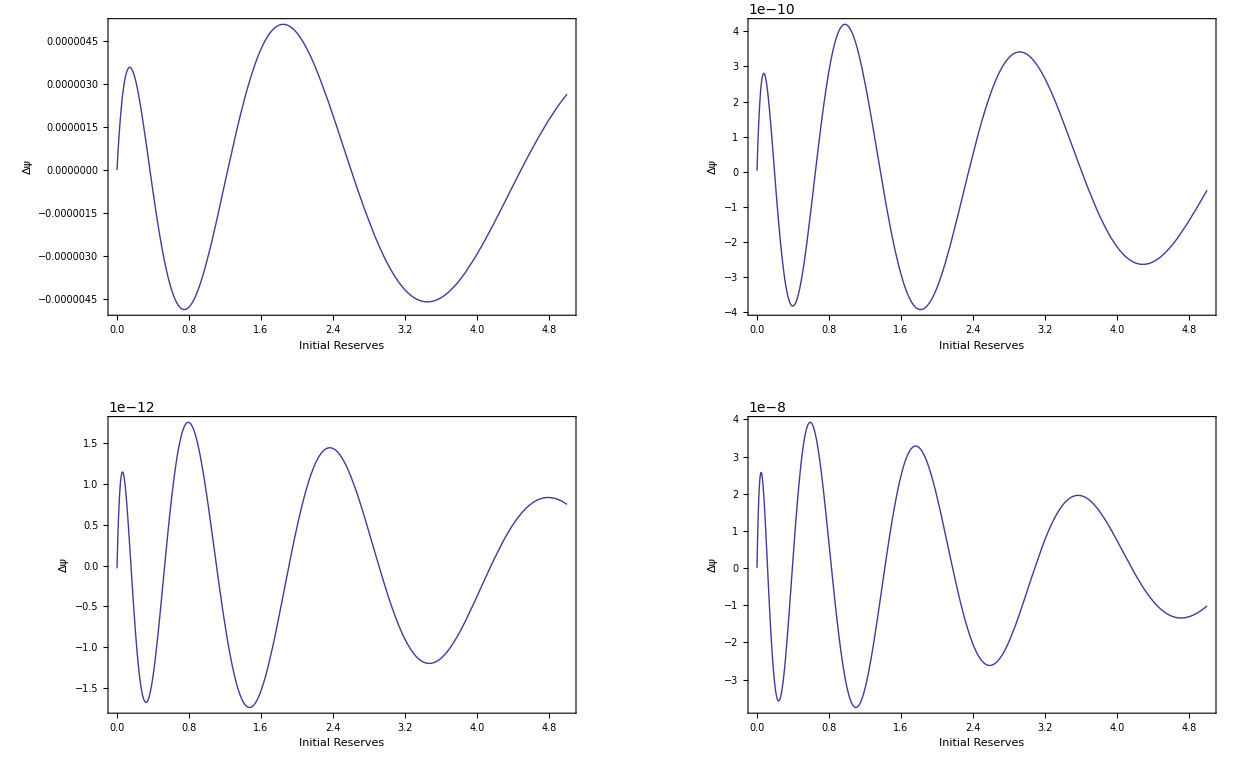

```mathematica
(*Graph Montrant les performance de la méthodes avec diférentes paramétrisation*)
GraphRuinProbabilityPolynomialComparison=Table[Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbabilityPolynomial[[i]],{u,0,5},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["m = "<>ParameterString[[i]],24]}},ImageSize->Large],{i,1,NbParametrization}];
GraphicsGrid[{{GraphRuinProbabilityPolynomialComparison[[1]],GraphRuinProbabilityPolynomialComparison[[2]]},{GraphRuinProbabilityPolynomialComparison[[3]],GraphRuinProbabilityPolynomialComparison[[4]]}}]
```

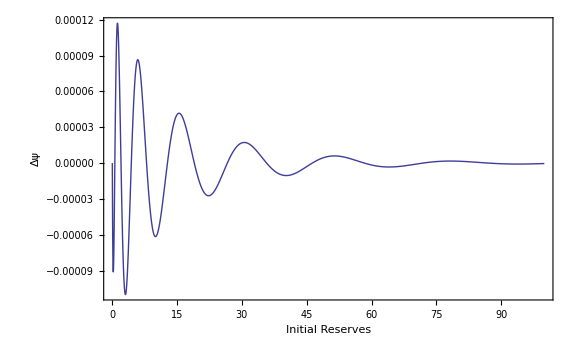

```mathematica
GraphRuinProbabilityPolynomial=Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbabilityPolynomial[[1]],{u,0,100},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Polynomial Expansion",24]}},ImageSize->Large]
```

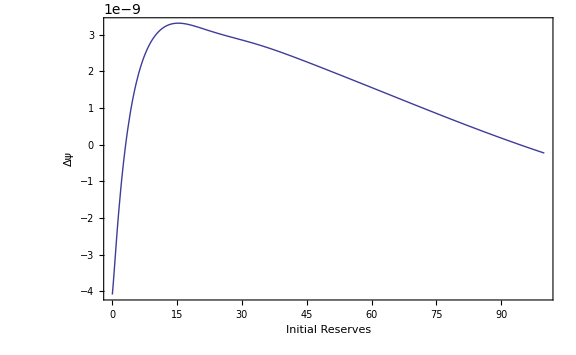

```mathematica
(*Calibration FFT*)
mFFT=11;
bFFT=18.5;
nFFT=15;
RuinProbaFFT=SurvivalNegBinPhaseTypeFFT[mFFT,bFFT,u,nFFT,1,p,α,T,e,k];
  GraphRuinProbaFFT=Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbaFFT,{u,0,100},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Fast Fourrier Transform",24]}},ImageSize->Large]
```

```mathematica
(*Calibration Mnats*)
αMnats=2000;
N[bMnats=Exp[1]];
N[VectorInitialReserves=Table[Log[αMnats/(αMnats-j+1)],{j,1,αMnats}]];
(*RuinProbabilityMnatsPersonal=Interpolation[Table[{Log[αMnats/(αMnats-i+1)]/Log[bMnats],N[RuinProbaPhaseTypeMnats[p,λ,c,α,T,t,k,αMnats,bMnats,i]]},{i,1,αMnats}]];*)
RuinMnatsGiven=Interpolation[Import["Documents/Article/RuinTheoryContribution/gamma3-120.txt","Table"][[2;;121,1;;2]]];
Import["Documents/Article/RuinTheoryContribution/gamma3-120.txt","Table"][[2;;121,1;;2]]
(*N[Table[RuinProbaPhaseTypeMnats2[p,λ,c,α,T,t,k,αMnats,VectorInitialReserves[[i]]],{i,1,αMnats}]]*)
(*N[Table[Sum[(-1)^(j)*LaplaceRuinProbaPhaseTypeMnats[i+Floor[αMnats*Exp[-VectorInitialReserves[[i]]]],p,λ,c,α,T,t,k]/j!
/(αMnats-Floor[αMnats*Exp[-VectorInitialReserves[[i]]]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-VectorInitialReserves[[i]]]]}],{i,1,αMnats}]]*)
(*N[Table[ψPhaseType[VectorInitialReserves[[i]],α,T,t,e,p],{i,1,αMnats}]]
Table[N[RuinProbaPhaseTypeMnats[p,λ,c,α,T,t,k,αMnats,bMnats,i]],{i,1,αMnats}]*)
(*N[Table[RuinProbaPhaseTypeMnats2[p,λ,c,α,T,e,k,αMnats,bMnats,VectorInitialReserves[[i]]],{i,1,αMnats}]]*)
(*N[Table[RuinProbaPhaseTypeMnats2[p,λ,c,α,T,t,e,k,αMnats,VectorInitialReserves[[i]]],{i,1,αMnats}]]*)
(*Import["Documents/Article/RuinTheoryContribution/gamma2-150.txt","Table"][[2;;121,2;;3]]*)
```

{{0,0.830989},{0.190115,0.821202},{0.381833,0.810959},{0.575184,0.800311},{0.770194,0.789311},{0.966893,0.778015},{1.16531,0.766476},{1.36547,0.754743},{1.56742,0.742862},{1.77117,0.730874},{1.97677,0.718815},{2.18425,0.706715},{2.39364,0.694603},{2.60498,0.6825},{2.8183,0.670427},{3.03364,0.658399},{3.25104,0.646429},{3.47055,0.634529},{3.6922,0.622707},{3.91603,0.610971},{4.14208,0.599326},{4.37041,0.587776},{4.60106,0.576326},{4.83407,0.564979},{5.0695,0.553735},{5.30739,0.542598},{5.5478,0.531568},{5.79078,0.520647},{6.03639,0.509834},{6.28468,0.499132},{6.53572,0.488539},{6.78956,0.478057},{7.04627,0.467685},{7.30592,0.457424},{7.56856,0.447274},{7.83428,0.437235},{8.10314,0.427307},{8.37522,0.41749},{8.6506,0.407785},{8.92936,0.398191},{9.21158,0.388709},{9.49735,0.379338},{9.78677,0.370078},{10.0799,0.36093},{10.3769,0.351894},{10.6778,0.34297},{10.9828,0.334157},{11.2919,0.325457},{11.6052,0.316868},{11.923,0.308391},{12.2452,0.300027},{12.5721,0.291774},{12.9038,0.283634},{13.2404,0.275606},{13.582,0.267691},{13.9288,0.259888},{14.2811,0.252198},{14.6389,0.24462},{15.0024,0.237155},{15.3718,0.229803},{15.7473,0.222564},{16.1291,0.215438},{16.5175,0.208425},{16.9126,0.201525},{17.3147,0.194739},{17.7241,0.188065},{18.1409,0.181506},{18.5656,0.17506},{18.9983,0.168727},{19.4395,0.162509},{19.8894,0.156404},{20.3484,0.150414},{20.8168,0.144537},{21.2951,0.138775},{21.7837,0.133127},{22.283,0.127593},{22.7936,0.122174},{23.3159,0.11687},{23.8504,0.111681},{24.3979,0.106607},{24.9589,0.101647},{25.5341,0.0968032},{26.1242,0.0920746},{26.7301,0.0874614},{27.3525,0.0829639},{27.9925,0.0785823},{28.6511,0.0743166},{29.3293,0.070167},{30.0284,0.0661338},{30.7497,0.062217},{31.4946,0.0584169},{32.2648,0.0547335},{33.062,0.0511673},{33.8882,0.0477182},{34.7456,0.0443865},{35.6367,0.0411725},{36.5641,0.0380763},{37.531,0.0350982},{38.5409,0.0322384},{39.5977,0.0294972},{40.7062,0.0268748},{41.8715,0.0243715},{43.0998,0.0219876},{44.3984,0.0197234},{45.7757,0.0175792},{47.2419,0.0155554},{48.8093,0.0136523},{50.4929,0.0118703},{52.3114,0.0102099},{54.2882,0.00867145},{56.4535,0.0072555},{58.8471,0.00596257},{61.523,0.00479328},{64.5566,0.00374828},{68.0587,0.00282833},{72.2008,0.00203431},{77.2703,0.00136725},{83.806,0.000828373},{93.0176,0.000419264},{108.765,0.000142048}}

```mathematica
N[RuinProbaPhaseTypeMnats2[p,λ,c,α,T,t,k,αMnats,6]]
```

0.000554378

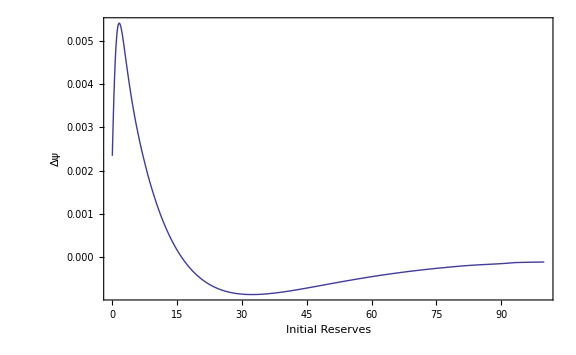

```mathematica
(*GraphRuinProbaMnats=Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbabilityMnatsPersonal[u],{u,0,5},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Scaled Laplace Transform",24]}},ImageSize->Large]*)
GraphRuinProbaMnats=Plot[ψPhaseType[u,α,T,t,e,p]-RuinMnatsGiven[u],{u,0,100},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Scaled Laplace Transform",24]}},ImageSize->Large]
(*GraphRuinProbaMnats=Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbaPhaseTypeMnats2[p,λ,c,α,T,t,k,αMnats,u],{u,0,5},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Scaled Laplace Transform",24]}},ImageSize->Large]
GraphRuinProbaMnats=DiscretePlot[ψPhaseType[u,α,T,t,e,p]-RuinProbabilityMnatsPersonal[u],{u,0,5},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Scaled Laplace Transform",24]}},ImageSize->Large]*)
```

0.376188

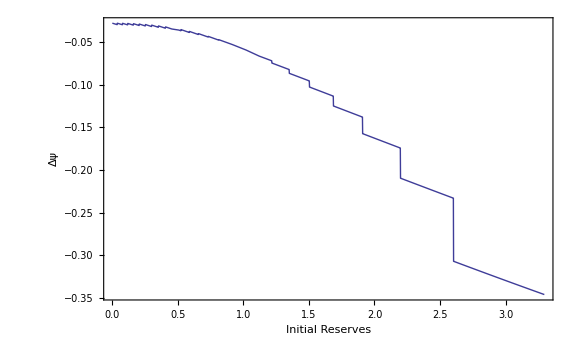

```mathematica
N[RuinProbaPhaseTypeMnats[p,λ,c,α,T,t,k,αMnats,bMnats,Log[αMnats/(αMnats-1+1)]/Log[bMnats]]]
```

```mathematica
(*Application algo de Panjer*)
h=1/10;
umax=100;
VectProbaUI=DiscretizePhaseType[α,T,e,umax,h];
VectProbaCompoundGeo=ProbaDiscreteGeometricCompoundPhaseType[p,h,VectProbaUI,umax];
```

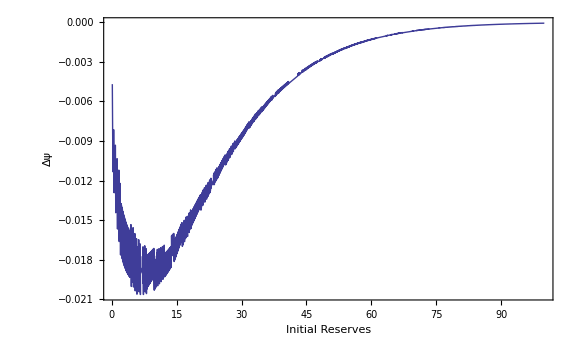

```mathematica
GraphRuinProbaPanjer=Plot[ψPhaseType[u,α,T,t,e,p]-RuinProbaPangerPhaseType[VectProbaCompoundGeo,h,u],{u,0.1,100},PlotRange->All,
LabelStyle->Directive[Black,24],Frame->True,FrameLabel->{{Style["Δψ",24],None},{Style["Initial Reserves",24],Style["Panjer's Algorithm",24]}},ImageSize->Large]
```

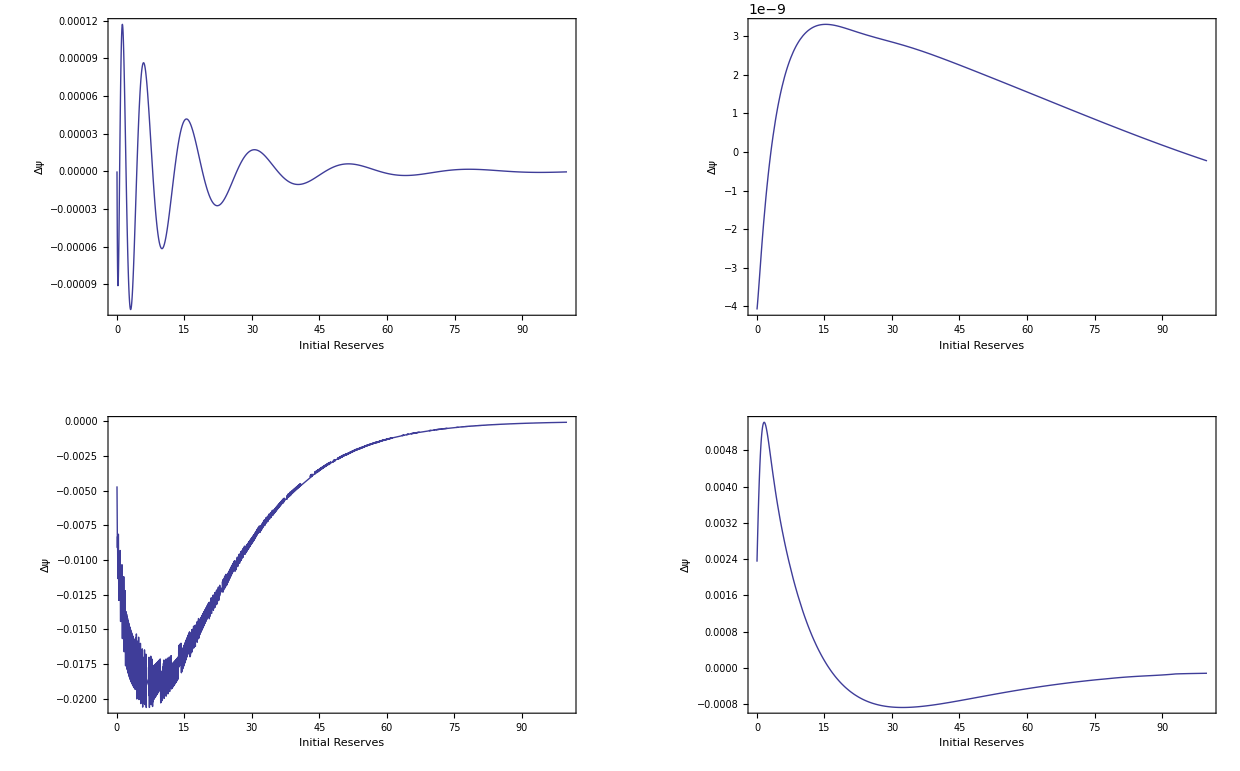

```mathematica
GraphicsGrid[{{GraphRuinProbabilityPolynomial,GraphRuinProbaFFT},{GraphRuinProbaPanjer,GraphRuinProbaMnats}}]
```

```mathematica
Max[N[CDFPhaseTypeI[α,T,e,-1]],0]
```

0